## 最佳平方逼近

```mathematica
a=-π/2;b=π/2;
inner[f_,g_]:=inner[f,g]=∫_a^b f g ⅆx
l[n_,x_]:=LegendreP[n,y]/.y->2/(b-a)x+(a+b)/(a-b)
LegendreApproximation[f_,n_]:=approx[f,n]=Collect[∑_(i=0)^n (inner[f,l[i,x]]l[i,x])/inner[l[i,x],l[i,x]],x]
```

0.9999999827823012 x-0.1666665152022362 x^3+0.008332964018218538 x^5-0.0001980475530092349 x^7+2.598110444084388×10^-6 x^9

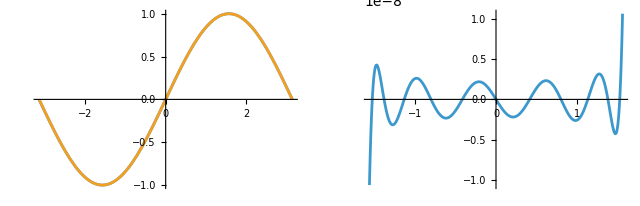

```mathematica
approxLegendre=LegendreApproximation[Sin[x],9];
N[approxLegendre,16]
GraphicsRow[{Plot[{ReleaseHold[approxLegendre],Sin[x]},{x,-π,π}],
Plot[ReleaseHold[approxLegendre]-Sin[x],{x,a,b}]}]
```

## 切比雪夫逼近

```mathematica
a=-π/2;b=π/2;
p[x_]:=1/(√(1-y^2))/.y->2/(b-a)x+(a+b)/(a-b)
weightedInner[f_,g_]:=weightedInner[f,g]=∫_a^b f g p[x]ⅆx
c[i_,x_]:=ChebyshevT[i,y]/.y->2/(b-a)x+(a+b)/(a-b)
ChebyshevApproximation[f_,n_]:=Collect[∑_(i=0)^n (weightedInner[f,c[i,x]]T[i])/weightedInner[c[i,x],c[i,x]],T]/.T[i_]:> HoldForm[c[i,x]]
```

1.133648177811748 c[1.,x]-0.1380717765871921 c[3.,x]+0.004490714246554918 c[5.,x]-0.00006770127584215249 c[7.,x]+5.891295330289313×10^-7 c[9.,x]

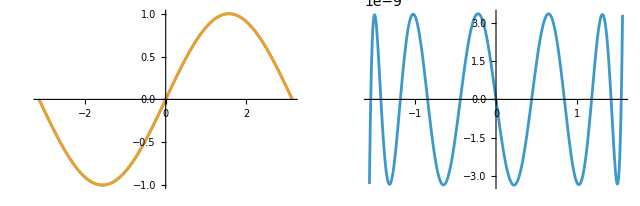

```mathematica
approxChebyshev=ChebyshevApproximation[Sin[x],9];
N[approxChebyshev,16]
GraphicsRow[{Plot[{ReleaseHold[approxChebyshev],Sin[x]},{x,-π,π}],
Plot[ReleaseHold[approxChebyshev]-Sin[x],{x,a,b}]}]
```

## 最佳一致逼近

```mathematica
(*The symbolic solution of such equation is nearly impossible*)BestUniformApproximation[func_,{var_,a_,b_},order_,opts:OptionsPattern[FindRoot]]:=Module[{f,p,e,g,coeffVars,extremaVars,extremaEqs,derivEqs,boundaryEqs,allVars,allEqs,solution,initialGuess},
f[x_]:=func/. var->x;
p[x_]:=Sum[c[i] x^i,{i,0,order}];
e[x_]:=f[x]-p[x];
g[x_]:=D[e[x],x];
coeffVars=Array[c,order+1,0];
extremaVars=Array[x,order];
extremaEqs=Table[(-1)^i e[x[i]]==e[a],{i,1,order}];
derivEqs=Table[g[x[i]]==0,{i,1,order}];
boundaryEqs={e[a]==(-1)^(order+1) e[b]};
allVars=Join[extremaVars,coeffVars];
allEqs=Join[extremaEqs,derivEqs,boundaryEqs];
initialGuess=Join[Table[{x[i],a+(b-a)*i/(order+1)},{i,1,order}],Table[{c[i],0},{i,0,order}]];
solution=FindRoot[allEqs,initialGuess,opts];
If[solution==={},Print["No solution found"];
Return[$Failed]];
Chop[p[var]/. solution]]
```

1.-0.5 x^2+0.0383867 x^4

1.-0.5 x^2+0.0383867 x^4

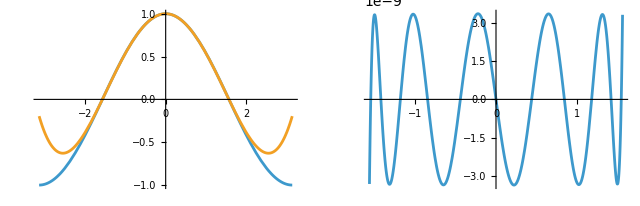

-Graphics-

```mathematica
approxUniform=BestUniformApproximation[Cos[x],{x,-π/2,π/2},4]
N[approxUniform,16]
GraphicsRow[{Plot[{ Cos[x],approxUniform},{x,-π,π}],Plot[ReleaseHold[approxChebyshev]-Sin[x],{x,a,b}]}]
```